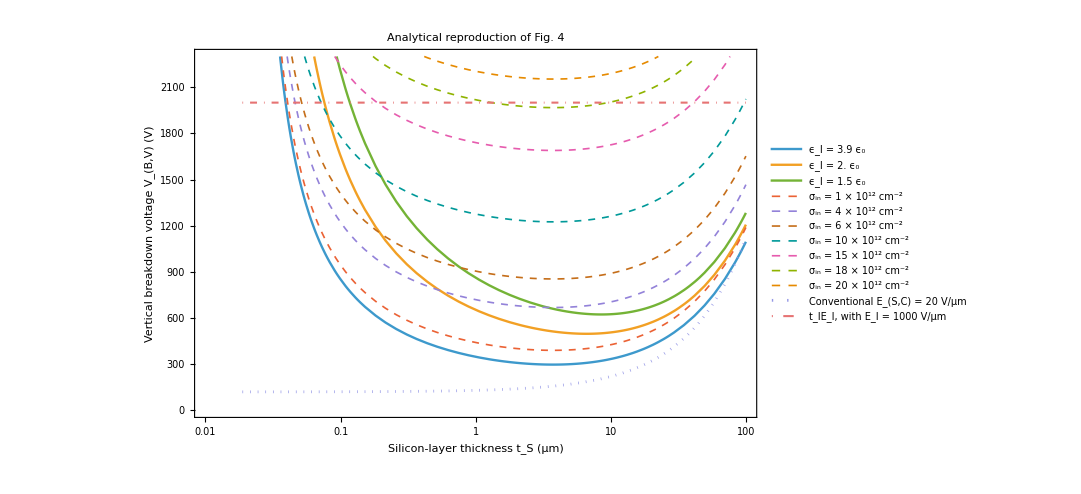

```mathematica
(* ============================================================*)(*Constants*)(* ============================================================*)q=1.602176634*10^-19;      (*electron charge,C*)
eps0=8.8541878128*10^-14;  (*vacuum permittivity,F/cm*)
epsSr=11.7;                  (*relative permittivity of silicon*)
tI=2.0;                      (*dielectric thickness,micrometers*)

(* ============================================================*)
(*Equation (10):Silicon critical electric field,V/um*)
(*tS must be in micrometers*)
(* ============================================================*)
siliconCriticalField[tS_]:=9.783*(21.765-Log[tS])/(Log[tS]+3.975);

(* ============================================================*)
(*Equation (13):Vertical breakdown voltage,V*)
(* ============================================================*)
verticalBreakdownVoltage[tS_,epsIr_,sigmaIn_]:=Module[{ESC,epsS,epsI,displacementVoltage,interfaceChargeVoltage},ESC=siliconCriticalField[tS];
epsS=epsSr*eps0;
epsI=epsIr*eps0;
(*First part:ESC*(epsS*tI+0.5*epsI*tS)/epsI*)displacementVoltage=ESC*(epsS*tI+0.5*epsI*tS)/epsI;
(*q*sigma/eps has units V/cm.tI in um is converted to cm using 10^-4*)interfaceChargeVoltage=q*sigmaIn*tI*10^-4/epsI;
displacementVoltage+interfaceChargeVoltage];

(*Conventional curve:ESC=20 V/um*)
conventionalVoltage[tS_]:=20.0*(0.5*tS+(epsSr/3.9)*tI);

(* ============================================================*)
(*Set Up Data Boundaries& Parameters*)
(* ============================================================*)
(*Equation (10) has a pole at exp(-3.975)=0.0188 um*)
pole=Exp[-3.975];
tSMin=1.001*pole;
tSMax=100.0;

(*Test cases defined in the Python script*)
permittivityCases={3.9,2.0,1.5};
sigmaCases={1,4,6,10,15,18,20}*10^12;

(*Generate arrays of expressions to plot*)
plotFunctions=Join[Table[verticalBreakdownVoltage[tS,epsIr,0],{epsIr,permittivityCases}],Table[verticalBreakdownVoltage[tS,3.9,sigma],{sigma,sigmaCases}],{conventionalVoltage[tS]},{tI*1000.0}];

(* ============================================================*)
(*Plot Formatting (Styles and Legends)*)
(* ============================================================*)
(*Dynamically generate formatted legend labels*)
legendLabels=Join[Table[Row[{Subscript["ϵ","I"]," = ",epsIr," ",Subscript["ϵ","0"]}],{epsIr,permittivityCases}],Table[Row[{Subscript["σ","in"]," = ",sigma/10^12," × ",Superscript["10","12"]," ",Superscript["cm","-2"]}],{sigma,sigmaCases}],{Row[{"Conventional ",Subscript["E","S,C"]," = 20 V/μm"}]},{Row[{Subscript["t","I"],Subscript["E","I"],", with ",Subscript["E","I"]," = 1000 V/μm"}]}];

(*Match the matplotlib visual styles*)
plotStyles=Join[Table[Directive[AbsoluteThickness[1.7]],{Length[permittivityCases]}],Table[Directive[Dashed,AbsoluteThickness[1.2]],{Length[sigmaCases]}],{Directive[Dotted,AbsoluteThickness[2]]},{Directive[DotDashed,AbsoluteThickness[1.5]]}];

(* ============================================================*)
(*Create Fig.4*)
(* ============================================================*)
LogLinearPlot[Evaluate[plotFunctions],{tS,tSMin,tSMax},PlotRange->{{0.01,100},{0,2300}},PlotStyle->plotStyles,(*Axis& Grid formatting*)Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted,Opacity[0.4]],FrameLabel->{Row[{"Silicon-layer thickness ",Subscript["t","S"]," (μm)"}],Row[{"Vertical breakdown voltage ",Subscript["V","B,V"]," (V)"}]},BaseStyle->{FontSize->12},PlotLabel->Style["Analytical reproduction of Fig. 4",14],(*Legend Configuration*)PlotLegends->Placed[LineLegend[legendLabels,LegendLayout->{"Column",2},LegendFunction->Framed,LabelStyle->{FontSize->10}],{0.75,0.75} (*Positions legend in the upper right quadrant*)],ImageSize->800]
```